```mathematica
F[m_,n_]:=Prepend[RandomInteger[{1,m},n],0]
```

```mathematica
F2[m_,n_]:=RandomInteger[{1,m},n]
```

```mathematica
G[m_,n_,c_]:=Table[FromContinuedFraction[F[m,n]],{c}]
```

```mathematica
G2[m_,n_,c_]:=Table[FromContinuedFraction[F2[m,n]],{c}]
```

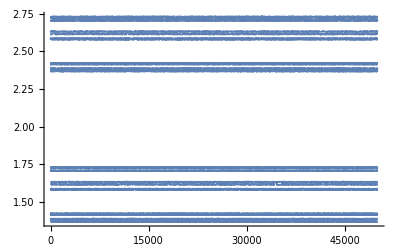

```mathematica
ListPlot[G2[2,50,50000]]
```

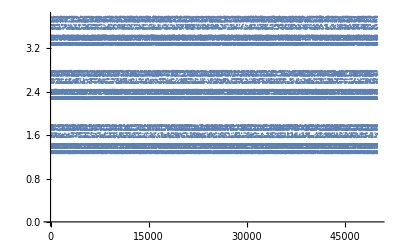

```mathematica
ListPlot[G2[3,30,50000]]
```

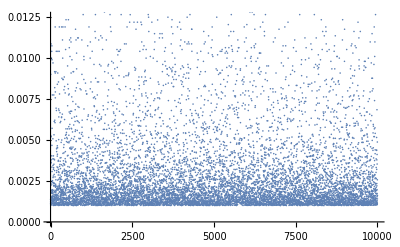

```mathematica
ListPlot[G[1000,150,10000]]
```